```mathematica
Solve[Sin[a]==Sin[b],a]
```

{{a→ConditionalExpression[π-ArcSin[Sin[b]]+2 π C[1],C[1]∈ℤ]},{a→ConditionalExpression[ArcSin[Sin[b]]+2 π C[1],C[1]∈ℤ]}}

```mathematica
%//Simplify
```

{{a→ConditionalExpression[π-ArcSin[Sin[b]]+2 π C[1],C[1]∈ℤ]},{a→ConditionalExpression[ArcSin[Sin[b]]+2 π C[1],C[1]∈ℤ]}}

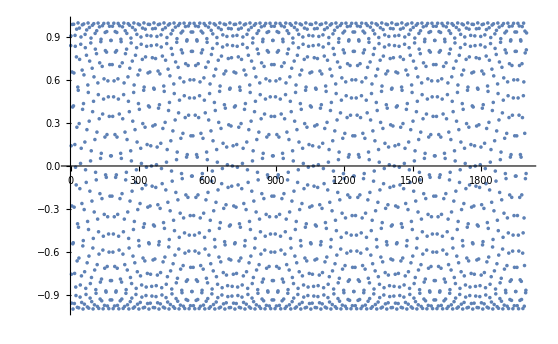

```mathematica
ListPlot[Sin/@Range[2000]]
```

```mathematica
Sin[9]-Sin[13]//N
```

-0.00804855

```mathematica
Sin[10]-Sin[12]//N
```

-0.00744819

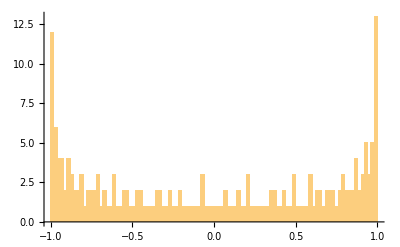

```mathematica
Histogram[Sin/@Range[200],100]
```

```mathematica
(527-273)
```

254

```mathematica
254/Pi//N
```

80.8507

```mathematica
254/81//N
```

3.1358

```mathematica
(881-171)/2
```

355

```mathematica
710/(2Pi)//N
```

113.

```mathematica
AGM=ArithmeticGeometricMean
```

ArithmeticGeometricMean

```mathematica
AGM[AGM[1,AGM[1,2]],AGM[2,AGM[1,2]]]-AGM[1,2]//N
```

0.000117531

```mathematica
f[AGM[1,x]]==(f[1]+f[x])/2
```

f[ArithmeticGeometricMean[1,x]]==1/2 (f[1]+f[x])

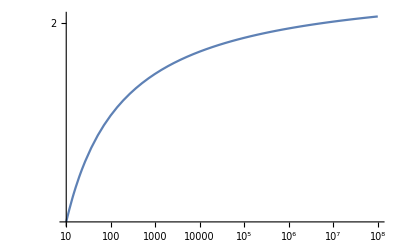

```mathematica
LogLogPlot[(ArithmeticGeometricMean[1,x]-(Pi x/(2Log[x])))/(-x/Log[x]^2),{x,10,10^8},PlotRange->All]
```

```mathematica
Limit[(ArithmeticGeometricMean[1,x]-(Pi x/(2Log[x])-Pi Log[2]x/Log[x]^2))/(-x/Log[x]^2),x->Infinity]
```

0

```mathematica
Limit[ArithmeticGeometricMean[1,x]-(Pi x/(2Log[x])-Pi Log[2]x/Log[x]^2),x->Infinity]
```

∞

```mathematica
Log10[AGM[1,10^1000.]]
```

996.833642795678